```mathematica
Quit[]
```

```mathematica
Start[]
```

Start[]

```mathematica
γ[s_] = {0,0,s};
γDerivative[s_] = D[γ[s],s];
```

```mathematica
BSIntegrand[x_,y_,z_,s_] = Cross[{x,y,z}-γ[s],γDerivative[s]]/(Norm[{x,y,z}-γ[s]])^3;
BSIntegrandCircle[r_,θ_,s_] = Cross[{r Cos[θ],r Sin[θ],0}-γ[s],γDerivative[s]]/(Norm[{r Cos[θ],r Sin[θ],0}-γ[s]])^3;
```

```mathematica
BSIntegrandCircle[r,θ,s]
```

{(r Sin[θ])/((Abs[s]^2+Abs[r Cos[θ]]^2+Abs[r Sin[θ]]^2)^(3/2)),-(r Cos[θ])/((Abs[s]^2+Abs[r Cos[θ]]^2+Abs[r Sin[θ]]^2)^(3/2)),0}

```mathematica
BSIIntegral[x_?NumericQ,y_?NumericQ,z_?NumericQ,a_?NumericQ,b_?NumericQ] := NIntegrate[BSIntegrand[x,y,z,s],{s,a,b},AccuracyGoal-> 6];
BSIIntegralCircle[r_?NumericQ,θ_?NumericQ,a_?NumericQ,b_?NumericQ] := NIntegrate[BSIntegrandCircle[r,θ,s],{s,a,b},AccuracyGoal-> 6];
```

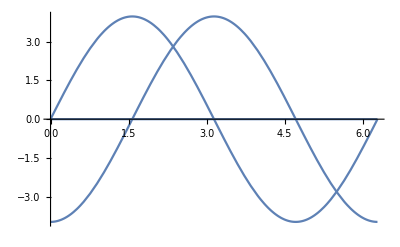

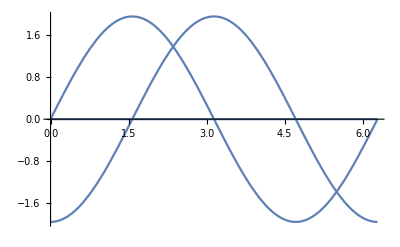

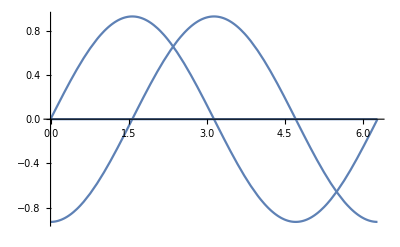

```mathematica
Plot[BSIIntegralCircle[1/2,θ,-5,5],{θ,0,2π}]
Plot[BSIIntegralCircle[1,θ,-5,5],{θ,0,2π}]
Plot[BSIIntegralCircle[2,θ,-5,5],{θ,0,2π}]
```

```mathematica
BSIIntegralCircleIntegral[r_?NumericQ,a_?NumericQ,b_?NumericQ] := NIntegrate[BSIntegrandCircle[r,θ,s],{s,a,b},{θ,0,2π},AccuracyGoal-> 6];
```

```mathematica
Chop[BSIIntegralCircleIntegral[1,-5,5]]
```

{0,0,0}

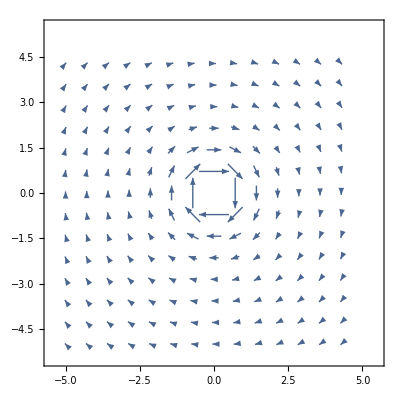

```mathematica
VectorPlot[Drop[BSIIntegral[x,y,0,-5,5],-1],{x,-5,5},{y,-5,5}]
```